```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
PtsBase=(Import["Profile_file_plas_2576.txt","Table"][[4;;-7]])[[All,{2,3}]]
```

{{-0.5,0},{-0.499969,0.000784591},{-0.499877,0.00156434},2570,{-0.499724,-0.00233445},{-0.499877,-0.00156434},{-0.499969,-0.000784591}}
 |  |  |  |

```mathematica
Pts=Reverse@Table[PtsBase[[q]],{q,1,Length[PtsBase],2}];
```

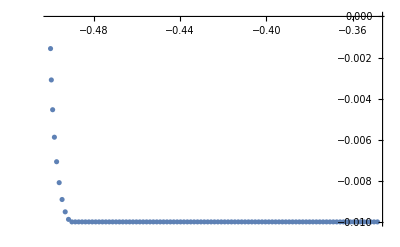

```mathematica
ListPlot[Pts[[1;;100]]]
```

```mathematica
n=Pts//Length
```

1288

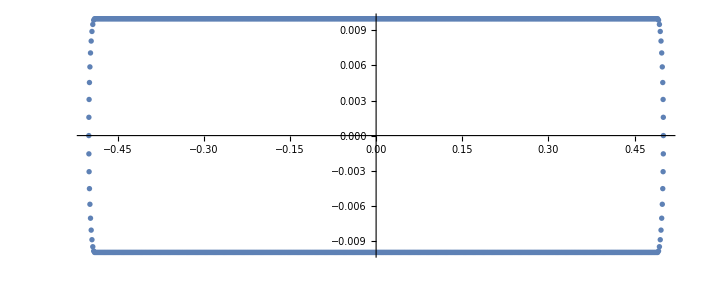

```mathematica
ListPlot[Pts,AspectRatio->Automatic]
```

```mathematica
Export["Blasius"<>ToString[n]<>".txt",{"#This is a textfile with points on Blasius airfoil"}~Join~{"np = "<>ToString[n]}~Join~{"r = { \\"}~Join~((ToString[#]<>", \\")&/@(Pts[[1;;-2]]))~Join~((ToString[#]<>" \\")&/@(Pts[[{-1}]]))~Join~{" }"}]
```

Blasius1288.txt